```mathematica
Quit[];
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.11 (2 Sep 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (6 Oct 2019)

by Thomas Hahn

```mathematica
(* Create my topologies. *)
(* 0 loops, 2 incoming legs, 2 outgoing legs.*)
topologies=CreateTopologies[0,2 -> 2];
_Hel=0;
Print[topologies];
```

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

loading generic model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_axialvector.gen

> $GenericMixing is OFF

generic model {DMsimp_s_spin1_axialvector} initialized

loading classes model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_axialvector.mod

> 46 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 147 vertices

> 48 counterterms of order 1

classes model {DMsimp_s_spin1_axialvector} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

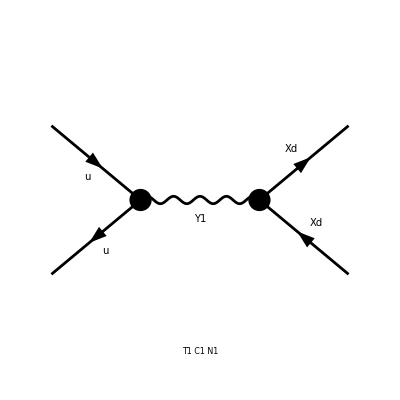

```mathematica
(* ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]} *)
diagvec=InsertFields[topologies,{F[7,{1}],-F[7,{1}]}->{F[13],-F[13]},InsertionLevel->{Classes},
Model->"DMsimp_s_spin1_axialvector",
GenericModel->"DMsimp_s_spin1_axialvector"];
Paint[diagvec];
```

```mathematica
(* Calculate amplitude. *)
ClearProcess[];
amplist = CreateFeynAmp[diagvec];
amp=CalcFeynAmp[amplist,FermionChains->VA];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/kpachal/fc-amp-9.frm

running FORM...

ok

```mathematica
(* Done with FeynArts! Time to pass the amplitude to FormCalc. *)
(* Squared matrix elements; evaluate *)
squared = SquaredME[amp];
Print[squared];
```

{FF[F1] (FFC[F1] Mat[F1,F1]+FFC[F2] Mat[F1,F2]+FFC[F3] Mat[F1,F3]+FFC[F4] Mat[F1,F4])+FF[F2] (FFC[F1] Mat[F2,F1]+FFC[F2] Mat[F2,F2]+FFC[F3] Mat[F2,F3]+FFC[F4] Mat[F2,F4])+FF[F3] (FFC[F1] Mat[F3,F1]+FFC[F2] Mat[F3,F2]+FFC[F3] Mat[F3,F3]+FFC[F4] Mat[F3,F4])+FF[F4] (FFC[F1] Mat[F4,F1]+FFC[F2] Mat[F4,F2]+FFC[F3] Mat[F4,F3]+FFC[F4] Mat[F4,F4]),{FF[F1]→1/4 (-gc154L+gc154R) (gc99L+gc99R) Den[S,MY1^2],FF[F2]→1/4 (-gc154L-gc154R) (gc99L+gc99R) Den[S,MY1^2],FF[F3]→1/4 Sub1 Den[S,MY1^2],FF[F4]→1/4 (gc154L+gc154R) (gc99L-gc99R) Den[S,MY1^2],FFC[F1]→1/4 (-(gc154LSuperscript[*])+gc154RSuperscript[*]) (gc99LSuperscript[*]+gc99RSuperscript[*]) Den[S,(MY1Superscript[*])^2],FFC[F2]→1/4 (-(gc154LSuperscript[*])-gc154RSuperscript[*]) (gc99LSuperscript[*]+gc99RSuperscript[*]) Den[S,(MY1Superscript[*])^2],FFC[F3]→1/4 (Sub1Superscript[*]) Den[S,(MY1Superscript[*])^2],FFC[F4]→1/4 (gc154LSuperscript[*]+gc154RSuperscript[*]) (gc99LSuperscript[*]-gc99RSuperscript[*]) Den[S,(MY1Superscript[*])^2]}}

```mathematica
(* SquaredME returns a list of {squared, squaredRules}, where we should later apply "squaredRules" to "squared". *)
(* Because of the quarks, we do ColorME too. *)
cleanSquaredME = squared[[1]]//.squared[[2]]//.HelicityME[amp]//FullSimplify
```

> 16 helicity matrix elements

preparing FORM code in /Users/kpachal/fc-hel-10.frm

running FORM...

ok

1/32 ((gc154L+gc154R) (gc99L-gc99R) ((T^2+2 MXd^2 (MXd^2+S-T-U)+U^2) (gc154LSuperscript[*]+gc154RSuperscript[*]) (gc99LSuperscript[*]-gc99RSuperscript[*])-S (-2 MXd^2+S+2 U) (gc154LSuperscript[*]-gc154RSuperscript[*]) (gc99LSuperscript[*]+gc99RSuperscript[*]))+(-gc154L+gc154R) (gc99L+gc99R) (S (-2 MXd^2+S+2 U) (gc154LSuperscript[*]+gc154RSuperscript[*]) (gc99LSuperscript[*]-gc99RSuperscript[*])+(2 MXd^4+T^2+U^2-2 MXd^2 (S+T+U)) (-(gc154LSuperscript[*])+gc154RSuperscript[*]) (gc99LSuperscript[*]+gc99RSuperscript[*]))+(-gc154L-gc154R) (gc99L+gc99R) (-(2 MXd^4+T^2+2 MXd^2 (S-T-U)+U^2) (gc154LSuperscript[*]+gc154RSuperscript[*]) (gc99LSuperscript[*]+gc99RSuperscript[*])+S (-2 MXd^2+S+2 U) (Sub1Superscript[*]))+Sub1 (-S (-2 MXd^2+S+2 U) (gc154LSuperscript[*]+gc154RSuperscript[*]) (gc99LSuperscript[*]+gc99RSuperscript[*])+(2 MXd^4+T^2+U^2-2 MXd^2 (S+T+U)) (Sub1Superscript[*]))) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* We want to sum over polarisations and make them go away: *)
TotalME = PolarizationSum[cleanSquaredME,GaugeTerms->False]//.Subexpr[]//.Abbr[]
```

preparing FORM code in /Users/kpachal/fc-pol-10.frm

running FORM...

ok

1/4 (gc99L ((-MXd^2 (2 gc154L (MXd^2-S)-gc154R S)+gc154L (-MXd^4+2 MXd^2 T+U^2)) (gc154LSuperscript[*])+(gc154L MXd^2 S-gc154R (-MXd^4+2 MXd^2 T-T^2)) (gc154RSuperscript[*])) (gc99LSuperscript[*])+gc99R ((gc154R MXd^2 S-gc154L (-MXd^4+2 MXd^2 T-T^2)) (gc154LSuperscript[*])+(MXd^2 (-2 gc154R (MXd^2-S)+gc154L S)+gc154R (-MXd^4+2 MXd^2 T+U^2)) (gc154RSuperscript[*])) (gc99RSuperscript[*])) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* Convert vertices back to versions we know *)
TotalMEFinalVertices = TotalME//. M$FACouplings
```

1/4 (gAu11 (gAu11Superscript[*]) ((-gAXd MXd^2 S-gAXd (-MXd^4+2 MXd^2 T-T^2)) (gAXdSuperscript[*])-(-MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)-gAXd (-MXd^4+2 MXd^2 T+U^2)) (gAXdSuperscript[*]))+gAu11 (gAu11Superscript[*]) (-(gAXd MXd^2 S+gAXd (-MXd^4+2 MXd^2 T-T^2)) (gAXdSuperscript[*])+(MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)+gAXd (-MXd^4+2 MXd^2 T+U^2)) (gAXdSuperscript[*]))) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* Sort out denominators. *)
TotalMEWithBWPropagator = TotalMEFinalVertices//.Den[a_,b_^2]Den[a_, Conjugate[b_]^2]:>1/((a - b^2)^2 + b^2 Gamma^2)
```

1/(4 (Gamma^2 MY1^2+(-MY1^2+S)^2))(gAu11 (gAu11Superscript[*]) ((-gAXd MXd^2 S-gAXd (-MXd^4+2 MXd^2 T-T^2)) (gAXdSuperscript[*])-(-MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)-gAXd (-MXd^4+2 MXd^2 T+U^2)) (gAXdSuperscript[*]))+gAu11 (gAu11Superscript[*]) (-(gAXd MXd^2 S+gAXd (-MXd^4+2 MXd^2 T-T^2)) (gAXdSuperscript[*])+(MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)+gAXd (-MXd^4+2 MXd^2 T+U^2)) (gAXdSuperscript[*])))

```mathematica
(* Tell Mathematica that my couplings, widths, and masses are positive real numbers *)
TotalMEClean = Refine[TotalMEWithBWPropagator, {Element[MY1,Reals],Element[gAXd,Reals],Element[gAu11,Reals],Element[Gamma,Reals], MY1>0, gVXd > 0, gVu11 > 0, Gamma >0}]
```

1/(4 (Gamma^2 MY1^2+(-MY1^2+S)^2))(gAu11^2 (gAXd (-gAXd MXd^2 S-gAXd (-MXd^4+2 MXd^2 T-T^2))-gAXd (-MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)-gAXd (-MXd^4+2 MXd^2 T+U^2)))+gAu11^2 (-gAXd (gAXd MXd^2 S+gAXd (-MXd^4+2 MXd^2 T-T^2))+gAXd (MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)+gAXd (-MXd^4+2 MXd^2 T+U^2))))

```mathematica
(* Full clean matrix element obtained. Testing begins here. *)
```

```mathematica
(* Define variables we'll need for next integrals. *)
(* Based on materials here: http://scipp.ucsc.edu/~haber/ph217/Lips.pdf *)
(* a,b->1,2 *)
LambdaXd = (S - 4 MXd^2)S
Lambdaq = (S - 4 Mq^2) S
PrefixDSigDOhm = 1/(64 Pi^2 S) Sqrt[LambdaXd]/Sqrt[Lambdaq]
PrefixDSigDT = 1/(16 Pi Lambdaq)
```

S (-4 MXd^2+S)

S (-4 Mq^2+S)

(√(S (-4 MXd^2+S)))/(64 π^2 S √(S (-4 Mq^2+S)))

1/(16 π S (-4 Mq^2+S))

```mathematica
(* Variant 1: we are going to convert everything into s and cos theta, then integrate out cos theta. *)
(* Use the massive substitutions for Mandelstam variables. *)
TVal = Mq^2 + MXd^2 - S/2 + 1/(2S) Sqrt[Lambdaq] Sqrt[LambdaXd] Cos[Theta]
METheta = TotalMEClean//.{T -> TVal, U-> 2 Mq^2 + 2 MXd^2 - S - T}
```

Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S)

1/(4 (Gamma^2 MY1^2+(-MY1^2+S)^2))(gAu11^2 (-gAXd (-MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)-gAXd (-MXd^4+(Mq^2+MXd^2-S/2-(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))))+gAXd (-gAXd MXd^2 S-gAXd (-MXd^4+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))-(Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2)))+gAu11^2 (gAXd (MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)+gAXd (-MXd^4+(Mq^2+MXd^2-S/2-(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))))-gAXd (gAXd MXd^2 S+gAXd (-MXd^4+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))-(Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2))))

```mathematica
(* We introduced Mq here so let's inform Mathematica about it too: *)
METhetaClean = Refine[METheta,{Element[Mq,Reals],Mq >0}]
```

1/(4 (Gamma^2 MY1^2+(-MY1^2+S)^2))(gAu11^2 (-gAXd (-MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)-gAXd (-MXd^4+(Mq^2+MXd^2-S/2-(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))))+gAXd (-gAXd MXd^2 S-gAXd (-MXd^4+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))-(Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2)))+gAu11^2 (gAXd (MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)+gAXd (-MXd^4+(Mq^2+MXd^2-S/2-(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))))-gAXd (gAXd MXd^2 S+gAXd (-MXd^4+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))-(Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2))))

```mathematica
(* From matrix element to cross section, using massive equation: *) 
dSigdOmega = PrefixDSigDOhm METhetaClean
Sigma1 = 2 Pi Integrate[dSigdOmega  Sin[Theta], {Theta, 0, Pi} ]
```

(√(S (-4 MXd^2+S)) (gAu11^2 (-gAXd (-MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)-gAXd (-MXd^4+(Mq^2+MXd^2-S/2-(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))))+gAXd (-gAXd MXd^2 S-gAXd (-MXd^4+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))-(Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2)))+gAu11^2 (gAXd (MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)+gAXd (-MXd^4+(Mq^2+MXd^2-S/2-(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))))-gAXd (gAXd MXd^2 S+gAXd (-MXd^4+2 MXd^2 (Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))-(Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2)))))/(256 π^2 S √(S (-4 Mq^2+S)) (Gamma^2 MY1^2+(-MY1^2+S)^2))

(gAu11^2 gAXd^2 √(S (-4 MXd^2+S)) (3 Mq^4+2 Mq^2 (5 MXd^2-2 S)+S (-4 MXd^2+S)))/(48 π (Gamma^2 MY1^2+(MY1^2-S)^2) S √(S (-4 Mq^2+S)))

```mathematica
(* Variant 2: we are going to convert everything into s and t, then integrate out t. *)
(* Keep the massive substitutions for Mandelstam variables. *)
MEMandelstamT = TotalMEClean//.{U-> 2 Mq^2 + 2 MXd^2 - S - T}
```

1/(4 (Gamma^2 MY1^2+(-MY1^2+S)^2))(gAu11^2 (-gAXd (-MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)-gAXd (-MXd^4+(2 Mq^2+2 MXd^2-S-T)^2+2 MXd^2 T))+gAXd (-gAXd MXd^2 S-gAXd (-MXd^4+2 MXd^2 T-T^2)))+gAu11^2 (gAXd (MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)+gAXd (-MXd^4+(2 Mq^2+2 MXd^2-S-T)^2+2 MXd^2 T))-gAXd (gAXd MXd^2 S+gAXd (-MXd^4+2 MXd^2 T-T^2))))

```mathematica
(* Again we introduced Mq here, so let's inform Mathematica about this one too: *)
MEMandelstamClean = Refine[MEMandelstamT,{Element[Mq,Reals],Mq >0}]
```

1/(4 (Gamma^2 MY1^2+(-MY1^2+S)^2))(gAu11^2 (-gAXd (-MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)-gAXd (-MXd^4+(2 Mq^2+2 MXd^2-S-T)^2+2 MXd^2 T))+gAXd (-gAXd MXd^2 S-gAXd (-MXd^4+2 MXd^2 T-T^2)))+gAu11^2 (gAXd (MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)+gAXd (-MXd^4+(2 Mq^2+2 MXd^2-S-T)^2+2 MXd^2 T))-gAXd (gAXd MXd^2 S+gAXd (-MXd^4+2 MXd^2 T-T^2))))

```mathematica
(* From matrix element to cross section: *)
dSigdt = PrefixDSigDT MEMandelstamClean
Sigma2 = Integrate[dSigdt, {T, -S, 0}]
```

(gAu11^2 (-gAXd (-MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)-gAXd (-MXd^4+(2 Mq^2+2 MXd^2-S-T)^2+2 MXd^2 T))+gAXd (-gAXd MXd^2 S-gAXd (-MXd^4+2 MXd^2 T-T^2)))+gAu11^2 (gAXd (MXd^2 (-2 gAXd (MXd^2-S)-gAXd S)+gAXd (-MXd^4+(2 Mq^2+2 MXd^2-S-T)^2+2 MXd^2 T))-gAXd (gAXd MXd^2 S+gAXd (-MXd^4+2 MXd^2 T-T^2))))/(64 π S (-4 Mq^2+S) (Gamma^2 MY1^2+(-MY1^2+S)^2))

-(gAu11^2 gAXd^2 (6 Mq^4+3 MXd^4+3 Mq^2 (4 MXd^2-S)-3 MXd^2 S+S^2))/(48 π (Gamma^2 MY1^2+(MY1^2-S)^2) (4 Mq^2-S))

```mathematica
(* Are these the same? *)
(* Clean up and find out. *)
Print[Sigma1]
CommonPart = 1/(-48Pi Sqrt[Lambdaq]Lambdaq ) gVu11^2 gVXd^2/(Gamma^2 MY1^2+(MY1^2-S)^2)
Sigma1Core = Sigma1 /CommonPart
Sigma2Core = Simplify[Sigma2/CommonPart]
```

```mathematica
(* Square both... *)
Sigma1CoreSq = Sigma1Core^2
Sigma2CoreSq = Sigma2Core^2
PossibleZero = Collect[ExpandAll[Sigma1CoreSq - Sigma2CoreSq],S]
```

```mathematica
(* OK, second format is by far the cleanest. Let's stick with that. *)
(* Do the integral. *)
TotalSigma = Integrate[Sigma2, S]
```

-((gAu11^2 gAXd^2 (2 MY1^2 (18 Mq^4+24 Mq^2 MXd^2+3 MXd^4+MY1^4+Gamma^2 (Mq^2+MY1^2)) ArcTan[(MY1^2-S)/(Gamma MY1)]+2 (24 Mq^6+48 Mq^4 MXd^2+3 MXd^2 MY1^2 (Gamma^2+MY1^2)+Mq^2 (12 MXd^4+7 MY1^4)) ArcTan[(-MY1^2+S)/(Gamma MY1)]-Gamma MY1 ((6 Mq^4-3 MXd^4+Gamma^2 MY1^2-8 Mq^2 MY1^2+MY1^4) Log[Gamma^2 MY1^2+(MY1^2-S)^2]+2 (10 Mq^4+3 MXd^4) Log[-4 Mq^2+S])))/(96 Gamma MY1 (16 Mq^4+Gamma^2 MY1^2-8 Mq^2 MY1^2+MY1^4) π))

```mathematica
(* We will drop terms with logs in them since these are pretty negligible. *)
SigmaTotApproximate = TotalSigma//.{Log[a_]->0}
```

-((gAu11^2 gAXd^2 (2 MY1^2 (18 Mq^4+24 Mq^2 MXd^2+3 MXd^4+MY1^4+Gamma^2 (Mq^2+MY1^2)) ArcTan[(MY1^2-S)/(Gamma MY1)]+2 (24 Mq^6+48 Mq^4 MXd^2+3 MXd^2 MY1^2 (Gamma^2+MY1^2)+Mq^2 (12 MXd^4+7 MY1^4)) ArcTan[(-MY1^2+S)/(Gamma MY1)]))/(96 Gamma MY1 (16 Mq^4+Gamma^2 MY1^2-8 Mq^2 MY1^2+MY1^4) π))

```mathematica
(* Equivalent of definite integral is SigmaTotApproximate|infinity - SigmaTotApproximate|2MXd *)
(* Limit not working so I am doing it myself. *)
DefiniteIntApproxUpper = SigmaTotApproximate//.{ArcTan[(MY1^2 -S)/(Gamma MY1)]->-Pi/2,ArcTan[(-MY1^2+S)/(Gamma MY1)]->Pi/2}
DefiniteIntApproxLower = SigmaTotApproximate//.{S->4MXd^2}
```

-((gAu11^2 gAXd^2 (-MY1^2 (18 Mq^4+24 Mq^2 MXd^2+3 MXd^4+MY1^4+Gamma^2 (Mq^2+MY1^2)) π+(24 Mq^6+48 Mq^4 MXd^2+3 MXd^2 MY1^2 (Gamma^2+MY1^2)+Mq^2 (12 MXd^4+7 MY1^4)) π))/(96 Gamma MY1 (16 Mq^4+Gamma^2 MY1^2-8 Mq^2 MY1^2+MY1^4) π))

-((gAu11^2 gAXd^2 (2 (24 Mq^6+48 Mq^4 MXd^2+3 MXd^2 MY1^2 (Gamma^2+MY1^2)+Mq^2 (12 MXd^4+7 MY1^4)) ArcTan[(4 MXd^2-MY1^2)/(Gamma MY1)]+2 MY1^2 (18 Mq^4+24 Mq^2 MXd^2+3 MXd^4+MY1^4+Gamma^2 (Mq^2+MY1^2)) ArcTan[(-4 MXd^2+MY1^2)/(Gamma MY1)]))/(96 Gamma MY1 (16 Mq^4+Gamma^2 MY1^2-8 Mq^2 MY1^2+MY1^4) π))

```mathematica
(* Finally, expression I want is difference of those. *)
FinalExpression = Simplify[DefiniteIntApproxUpper - DefiniteIntApproxLower]
```

(gAu11^2 gAXd^2 (MY1^2 (18 Mq^4+24 Mq^2 MXd^2+3 MXd^4+MY1^4+Gamma^2 (Mq^2+MY1^2)) π-(24 Mq^6+48 Mq^4 MXd^2+3 MXd^2 MY1^2 (Gamma^2+MY1^2)+Mq^2 (12 MXd^4+7 MY1^4)) π+2 (24 Mq^6+48 Mq^4 MXd^2+3 MXd^2 MY1^2 (Gamma^2+MY1^2)+Mq^2 (12 MXd^4+7 MY1^4)) ArcTan[(4 MXd^2-MY1^2)/(Gamma MY1)]+2 MY1^2 (18 Mq^4+24 Mq^2 MXd^2+3 MXd^4+MY1^4+Gamma^2 (Mq^2+MY1^2)) ArcTan[(-4 MXd^2+MY1^2)/(Gamma MY1)]))/(96 Gamma MY1 (16 Mq^4+Gamma^2 MY1^2-8 Mq^2 MY1^2+MY1^4) π)

```mathematica
(* One way to clean this up: arctan(-x) = - arctan(x) *)
CleanFinal = Simplify[FinalExpression//.ArcTan[(-4MXd^2 + MY1^2)/(Gamma MY1)]->-ArcTan[(4MXd^2 - MY1^2)/(Gamma MY1)]]
```

(gAu11^2 gAXd^2 (-24 Mq^6-6 Mq^4 (8 MXd^2-3 MY1^2)+Mq^2 (-12 MXd^4+Gamma^2 MY1^2+24 MXd^2 MY1^2-7 MY1^4)+MY1^2 (3 MXd^4-3 MXd^2 MY1^2+MY1^4+Gamma^2 (-3 MXd^2+MY1^2))) (π-2 ArcTan[(4 MXd^2-MY1^2)/(Gamma MY1)]))/(96 Gamma MY1 (16 Mq^4+Gamma^2 MY1^2-8 Mq^2 MY1^2+MY1^4) π)

```mathematica
(* In case I need more simplification, drop Mq: *)
CleanFinalSimple = CleanFinal//.Mq->0
```

(gAu11^2 gAXd^2 MY1 (3 MXd^4-3 MXd^2 MY1^2+MY1^4+Gamma^2 (-3 MXd^2+MY1^2)) (π-2 ArcTan[(4 MXd^2-MY1^2)/(Gamma MY1)]))/(96 Gamma (Gamma^2 MY1^2+MY1^4) π)

```mathematica
(* OK, that looks non-terrible. Gamma in the demoninator is a non-issue since this is total width, not Gamma_DM *)
(* Let's do a few checks: what does it simplify down to in on-shell and off-shell cases? *)
(* Very on-shell: MY1 >> MXd. Let initial and final state masses both go to zero. *)
(* MY1 >> Gamma also, so ArcTan[MY1/Gamma] -> Pi/2 *)
OnShellLimit = CleanFinal//.{MXd -> 0, Mq->0, ArcTan[MY1/Gamma]-> Pi/2}
```

```mathematica
(* Very off-shell: MY1 << 2 MXd. *)
(* This will make Mathematica barf without some help on the arctan. *)
OffShellLimit = CleanFinal//.{ArcTan[(4 MXd^2 - MY1^2)/(Gamma MY1)]-> -Pi/2, MY1->0}
```